(2 D^2 ⅇ^(D/(k T)))/((2+ⅇ^(D/(k T)))^2 k T^2)

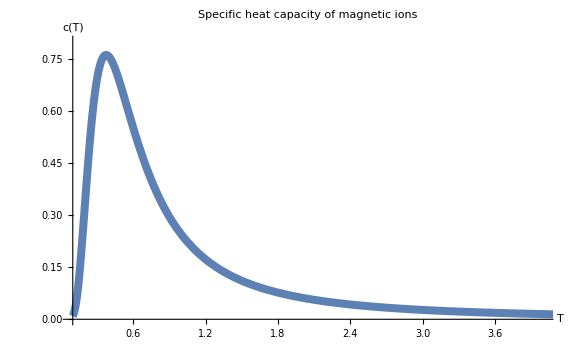

```mathematica
c[T_]:=(2*D^2*Exp[D/(k*T)])/(k*T^2(2+Exp[D/(k*T)])^2);
c[T]

Plot[{c[T]/.k->1/.D->1} ,{T,0.1,5},
PlotStyle->{Directive[Thickness[0.01]]},  AxesLabel->{Style["T",16],Style["c(T)",16]},
PlotLabel->Style["Specific heat capacity of magnetic ions", Black, FontSize->20], 
ImageSize->Large, PlotRange->{{0.1,4},{0,0.8}}, TicksStyle->Opacity[0]]
```